# BBE Project

Denizhan Pak

## Initialization

```mathematica
ClearAll["Global`*"]
```

Update this path to reflect the location of this file on your computer

```mathematica
<<"/home/naxicon/.Mathematica/Applications/Dynamica.m"
```

Dynamica (Version 1.0.10 - 9/14/2020), Copyright(c) 1993-2020 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
σ[x_]:=1/(1+ⅇ^-x)
```

```mathematica
f1[y0_,y1_,y2_,y3_,y4_]:=1/4.46684594 *(-y3+-7.32674007 *σ[y0+-2.85244578]+10.8000867 *σ[y1+1.79864592]+-11.1531948* σ[y2+-11.4560575])
```

```mathematica
f2[y0_,y1_,y2_,y3_,y4_]:=1/1.5163529* (-y4+6.27124276 * σ[y0+-2.85244578]+-3.52103606 * σ[y1+1.79864592]+3.24680276 * σ[y2+-11.4560575])
```

```mathematica
F[{y3_,y4_},{y2_,y0_,y1_}]:= {f1[y0,y1,y2,y3,y4], f2[y0,y1,y2,y3,y4]}
```

```mathematica
B[{xdot_},{y2_,y0_,y1_,y3_,y4_}]:= {-(f1[y0,y1,y2,y3,y4]- f2[y0,y1,y2,y3,y4])}
```

```mathematica
Motors= DynamicalSystem[F[{y3,y4},{y0,y1,y2}], {{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}]
```

DynamicalSystem[«2 ODEs»,{y3,y4},{y0,y1,y2}]

```mathematica
Behavior=DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,-4,4}}, {{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]
```

DynamicalSystem[«1 ODE»,{xdot},{y3,y4,y0,y1,y2}]

DynamicalSystem[«2 ODEs»,{y3,y4},{y0→-5,y1→-5,y2→-5}]

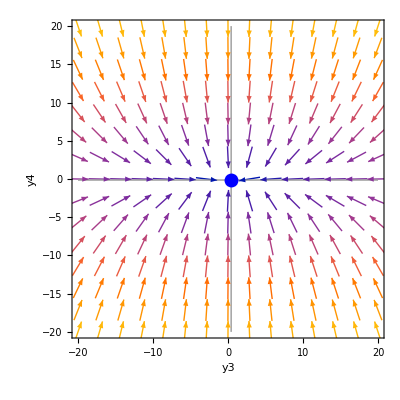

```mathematica
Mplot= Motors/.{y2->-5,y1->-5,y0->-5}
Show[DisplayVectorField[Mplot],DisplayPhasePortrait[Mplot, SaddleManifolds->True,NullManifolds->True]]
```

```mathematica
Mplot
```

DynamicalSystem[«2 ODEs»,{y3,y4},{y0→-5,y1→-5,y2→-5}]

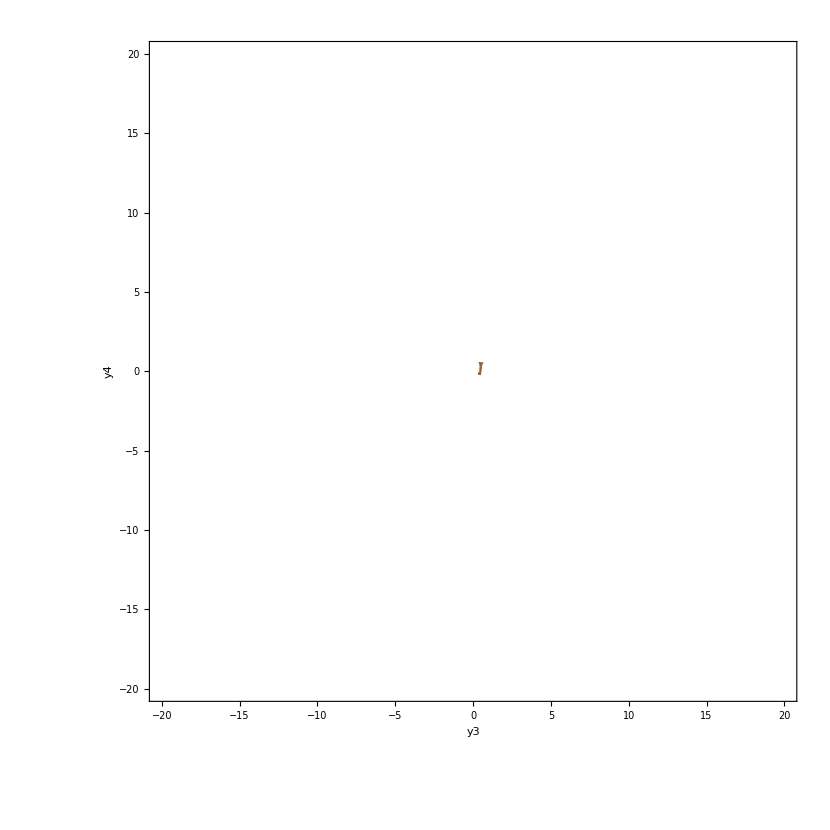

```mathematica
DisplayTrajectories[Mplot,{{0.5,0.5}},1000]
```

```mathematica
Manipulate[
DisplayPhasePortrait[DS/.{y2->$y2,y1->$y1,y0->$y0}, SaddleManifolds->True,NullManifolds->True],{{$y0,0},-20,10},{{$y1,0},-20,10},{{$y2,0},-20,10}]
```

```mathematica
Manipulate[DisplayPhasePortrait[DS/.{y2->0,y1->0,y0->$y3}, SaddleManifolds->True,NullManifolds->True],{$y3,-20,5}]
$PhasePortraitEPs
DisplayVectorField[DS]
```

{EquilibriumPoint[Stable,Node,{9.26618,-3.02096}]}

Too many free parameters for DisplayVectorField: {y0,y1,y2}

{}

Part::partw: Part 6 of DynamicalSystem[-0.223872 (-11.1532/(1+Power[«2»])-7.32674/(1+Power[«2»])+10.8001/(1+Power[«2»])-y3)+0.659477 (3.2468/(1+Power[«2»])+6.27124/(1+Power[«2»])-3.52104/(1+Power[«2»])-y4),{{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

Complement::heads: Heads Part and List at positions 2 and 1 are expected to be the same.

Invalid parameters Complement[{y2,y1,y0},DynamicalSystem[-0.223872 (-11.1532/(1+ⅇ^(11.4561-y0))-7.32674/(1+ⅇ^(2.85245-y1))+10.8001/(1+ⅇ^(-1.79865-y2))-y3)+0.659477 (3.2468/(1+ⅇ^(11.4561-y0))+6.27124/(1+ⅇ^(2.85245-y1))-3.52104/(1+ⅇ^(-1.79865-y2))-y4),{{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦6⟧] for DynamicalSystem[-0.223872 (-11.1532/(1+ⅇ^(11.4561-y0))-7.32674/(1+ⅇ^(2.85245-y1))+10.8001/(1+ⅇ^(-1.79865-y2))-y3)+0.659477 (3.2468/(1+ⅇ^(11.4561-y0))+6.27124/(1+ⅇ^(2.85245-y1))-3.52104/(1+ⅇ^(-1.79865-y2))-y4),{{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}]

Part::partw: Part 9 of DynamicalSystem[-0.223872 (-11.1532/(1+Power[«2»])-7.32674/(1+Power[«2»])+10.8001/(1+Power[«2»])-y3)+0.659477 (3.2468/(1+Power[«2»])+6.27124/(1+Power[«2»])-3.52104/(1+Power[«2»])-y4),{{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

ReplaceAll::reps: {DynamicalSystem[-0.223872 (-11.1532 Power[«2»]-7.32674 Power[«2»]+10.8001 Power[«2»]-y3)+0.659477 (3.2468 Power[«2»]+6.27124 Power[«2»]-3.52104 Power[«2»]-y4),{{y3,-20,20},{y4,-20,20}},{{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦9⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Too many free parameters for DisplayPhasePortrait: {y0,y1,y2,y3,y4}

Part::partw: Part 6 of DynamicalSystem[B[{xdot},{y0,y1,y2}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

Complement::heads: Heads Part and List at positions 2 and 1 are expected to be the same.

Invalid parameters Complement[{y2,y1,y0},DynamicalSystem[B[{xdot},{y0,y1,y2}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦6⟧] for DynamicalSystem[B[{xdot},{y0,y1,y2}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]

Part::partw: Part 9 of DynamicalSystem[B[{xdot},{y0,y1,y2}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

ReplaceAll::reps: {DynamicalSystem[B[{xdot},{y0,y1,y2}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦9⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Too many free parameters for DisplayPhasePortrait: {xdot,y0,y1,y2,y3,y4}

Part::partw: Part 6 of DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

Complement::heads: Heads Part and List at positions 2 and 1 are expected to be the same.

Invalid parameters Complement[{y2,y1,y0},DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦6⟧] for DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]

Part::partw: Part 9 of DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}] does not exist.

ReplaceAll::reps: {DynamicalSystem[B[{xdot},{y0,y1,y2,y3,y4}],{{xdot,0},-4,4},{{y3,-20,20},{y4,-20,20},{y0,-20,5},{y1,-20,5},{y2,-20,5}}]⟦9⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Too many free parameters for DisplayPhasePortrait: {xdot,y0,y1,y2,y3,y4}

Too many free parameters for DisplayPhasePortrait: {y3,y4}

Too many free parameters for DisplayPhasePortrait: {y3,y4}

Too many free parameters for DisplayPhasePortrait: {y3,y4}

```mathematica
Manipulate[
DisplayFlow[DS/.{y2->$y2,y1->$y1,y0->$y0,y3->0,y4->0}, 5],{{$y0,0},-20,10},{{$y1,0},-20,10},{{$y2,0},-20,10}]
```